# Homework 15

## Problem 15.1

A ray of light passes near a hot road. The index of refraction is given by the function n(y)=1+alpha*y, where y is the height above the road and alpha is a positive constant that will be set later.

We will use Fermat's principle (Eq. 6.3) and the Euler-Lagrange Equation (Eq. 6.13) to find the path of light initially at y=20 m and traveling in a direction 33 degrees below the horizontal.

First, we write the integrand f as a function of y and yp=dy/dx so we can take the appropriate derivatives. (See Eq.6.3). 
Hint: Fermat’s principle says the path will minimize the time for the light to travel from one point to another. Express dt in terms of v and ds, where ds is an incremental displacement. Using Eq. 6.1 for ds and the fact that v = c/n, you can now write the integrand in the appropriate form.

```mathematica
Quit[]
```

```mathematica
c=2.998*10^8;
n=1+alpha*y;
f=n/c+yp^2;
```

### Solutions

The correct expressions are:
n=1+α*y
f=n/c*√(1+y'[x]^2)=n/c*√(1+yp^2)

Now we take the derivatives found in the Euler Lagrange expression and substitute functional expressions for them. I’ll take care of this for you.

```mathematica
dfdy=D[f,y]/.{y->y[x],yp->y'[x]}
dfdyp=D[f,yp]/.{y->y[x],yp->y'[x]}
```

3.33556×10^-9 alpha

2 y'[x]

Now write the Euler - Lagrange equation in terms of dfdy and dfdyp.

```mathematica
eq1=dfdy-D[dfdyp,x]==0
```

3.33556×10^-9 alpha-2 y''[x]==0

### Solutions

The correct equation is:
df/dy - d/dx [df/dy']=0

To solve the equation, you' ll need the boundary conditions.
y(0)=y0
y’(0)=yp0
We also set alpha to 0.01. (You can play around with this value later to see how it affects the trajectory.)

```mathematica
DSolve[eq1,y[x],x]
```

{{y[x]→8.33889×10^-10 alpha x^2+C[1]+x C[2]}}

```mathematica
solved[x]=DSolve[eq1,y[x],x]
```

{{y[x]→8.33889×10^-10 alpha x^2+C[1]+x C[2]}}

```mathematica
g[x]=y[x]/.%
```

{8.33889×10^-10 alpha x^2+C[1]+x C[2]}

```mathematica
g1[x]=D[g[x],x]
```

{1.66778×10^-9 alpha x+C[2]}

```mathematica
D[g1[x],x]
```

{1.66778×10^-9 alpha}

```mathematica
N[-Tan[33 Degree]]
```

-0.649408

```mathematica
-Tan[0]
```

0

```mathematica
y0=20;
yp0=-Tan[33 Degree];
alpha=0.01;
```

### Hint

For the initial condition on y’(x), you'll need to specify the initial slope (dy/dx) of the ray. This is dy/dx = -tan (33 degrees).

Now we solve the equation numerically and plot the result.

{{y→InterpolatingFunction[…]}}

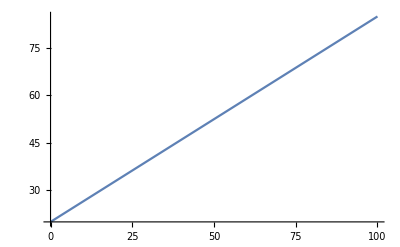

```mathematica
s=NDSolve[{eq1,y[0]==y0,y'[0]==yp0},y,{x,0,100}]
Plot[Evaluate[y[x]/.s],{x,0,100}]
```

### Solutions

For the initial conditions and value of alpha stated in the problem, the trajectory of the light ray is:
-Graphics-

## Written Problems